## Sinobit from DXF exported from Eagle CAD

See stackexchange for details

```mathematica
SetDirectory["~/scad/Maerklin/mechanical"]
```

/home/cmaier/scad/Maerklin/mechanical

```mathematica
feilen=FileNames["sinobit_*.dxf"]
```

{sinobit_v1.0.dxf,sinobit_v1.1.dxf}

```mathematica
Import[#,{"DXF","Elements"}]&/@feilen
```

{{BoundaryMeshRegion,CoordinateTransform,Graphics3D,GraphicsComplex,LineData,LineObjects,MeshRegion,PlotRange,PointData,PointObjects,PolygonData,PolygonObjects,Region,Summary,VertexColors,VertexData,ViewPoint},{BoundaryMeshRegion,CoordinateTransform,Graphics3D,GraphicsComplex,LineData,LineObjects,MeshRegion,PlotRange,PointData,PointObjects,PolygonData,PolygonObjects,Region,Summary,VertexColors,VertexData,ViewPoint}}

```mathematica
rawdata=Import[#,{"DXF",{"LineObjects","PointObjects","PolygonObjects"}}]&/@feilen;
```

```mathematica
Dimensions[rawdata]
```

{2,3}

```mathematica
Dimensions/@rawdata
```

{{3},{3}}

```mathematica
Map[Dimensions,rawdata,{2}]
```

{{{1174},{0},{0}},{{1176},{0},{0}}}

```mathematica
Graphics3D[rawdata⟦1⟧]
```

-Graphics3D-

```mathematica
Graphics3D[rawdata⟦2⟧]
```

-Graphics3D-

### Outlines

Educated guess: the first line is the outline

```mathematica
Graphics3D[rawdata⟦1,1,1⟧]
```

-Graphics3D-

```mathematica
Graphics3D[rawdata⟦2,1,1⟧]
```

-Graphics3D-

#### Outline data

```mathematica
First[First[#]]&/@rawdata
```

{Line[{{-12.6492,0.867697,0},{-12.6412,0.681553,0},{-12.6168,0.494794,0},{-12.5762,0.310872,0},{-12.5197,0.131188,0},{-12.4478,-0.0428938,0},{-12.361,-0.210041,0},{-12.2599,-0.368988,0},{-12.1454,-0.518525,0},{-12.0183,-0.657509,0},{13.6676,-26.3918,0},{13.669,-26.3932,0},{13.8079,-26.5205,0},{13.9573,-26.6352,0},{14.1162,-26.7363,0},{14.2832,-26.8233,0},{14.4573,-26.8954,0},{14.6369,-26.952,0},{14.8208,-26.9928,0},{15.0075,-27.0174,0},{15.1957,-27.0256,0},{51.5063,-27.0256,0},{51.6945,-27.0173,0},{51.8812,-26.9926,0},{52.0651,-26.9518,0},{52.2447,-26.8951,0},{52.4187,-26.8229,0},{52.5857,-26.7358,0},{52.7445,-26.6346,0},{52.8939,-26.5198,0},{53.0327,-26.3925,0},{78.8802,-0.520663,0},{78.9844,-0.406897,0},{79.0789,-0.283841,0},{79.1622,-0.153019,0},{79.2338,-0.0154344,0},{79.2932,0.127869,0},{79.3398,0.2758,0},{79.3734,0.427234,0},{79.3936,0.581019,0},{79.4004,0.735981,0},{79.4004,37.2074,0},{79.3924,37.3936,0},{79.368,37.5804,0},{79.3274,37.7643,0},{79.2709,37.944,0},{79.199,38.118,0},{79.1122,38.2852,0},{79.0111,38.4441,0},{78.8966,38.5937,0},{78.7695,38.7327,0},{53.109,64.441,0},{53.1076,64.4424,0},{52.9687,64.5697,0},{52.8193,64.6843,0},{52.6604,64.7855,0},{52.4934,64.8725,0},{52.3194,64.9446,0},{52.1397,65.0012,0},{51.9558,65.042,0},{51.7691,65.0666,0},{51.5809,65.0748,0},{15.2701,65.0748,0},{15.0829,65.0667,0},{14.8962,65.0422,0},{14.7123,65.0015,0},{14.5326,64.9449,0},{14.3586,64.8729,0},{14.1915,64.7861,0},{14.0326,64.6849,0},{13.8831,64.5703,0},{13.7442,64.4432,0},{-12.0161,38.7071,0},{-12.0168,38.7064,0},{-12.1441,38.5675,0},{-12.2588,38.4181,0},{-12.36,38.2592,0},{-12.4469,38.0922,0},{-12.519,37.9181,0},{-12.5756,37.7385,0},{-12.6164,37.5546,0},{-12.641,37.3679,0},{-12.6492,37.1797,0},{-12.6492,0.867697,0},{-12.6492,0.867697,0}}],Line[{{-12.6492,1.36683,0},{-12.6366,1.07904,0},{-12.599,0.793438,0},{-12.5367,0.512203,0},{-12.4501,0.237472,0},{-12.3398,-0.0286625,0},{-12.2068,-0.284178,0},{-12.052,-0.527128,0},{-11.8767,-0.755663,0},{-11.6832,-0.966944,0},{13.3837,-26.0574,0},{13.596,-26.2521,0},{13.8244,-26.4276,0},{14.0673,-26.5824,0},{14.3228,-26.7156,0},{14.5888,-26.8259,0},{14.8635,-26.9127,0},{15.1447,-26.9752,0},{15.4303,-27.0129,0},{15.7181,-27.0256,0},{15.7196,-27.0256,0},{51.0814,-27.0256,0},{51.3692,-27.013,0},{51.6548,-26.9754,0},{51.9361,-26.9131,0},{52.2108,-26.8265,0},{52.4769,-26.7162,0},{52.7324,-26.5832,0},{52.9754,-26.4284,0},{53.2039,-26.2531,0},{53.4163,-26.0585,0},{53.4185,-26.0563,0},{78.4355,-0.992156,0},{78.6299,-0.779591,0},{78.805,-0.550891,0},{78.9596,-0.307797,0},{79.0923,-0.0521563,0},{79.2023,0.214084,0},{79.2887,0.488894,0},{79.3508,0.770188,0},{79.3881,1.05582,0},{79.4004,1.34051,0},{79.4004,36.706,0},{79.3878,36.9937,0},{79.3502,37.2793,0},{79.2879,37.5606,0},{79.2013,37.8353,0},{79.091,38.1014,0},{78.958,38.357,0},{78.8032,38.5999,0},{78.6279,38.8284,0},{78.4333,39.0408,0},{78.4322,39.0419,0},{53.3417,64.1088,0},{53.1293,64.3033,0},{52.9007,64.4785,0},{52.6576,64.6332,0},{52.4021,64.7661,0},{52.1359,64.8762,0},{51.8611,64.9627,0},{51.5798,65.0249,0},{51.2942,65.0624,0},{51.008,65.0748,0},{15.6443,65.0748,0},{15.3566,65.0622,0},{15.071,65.0246,0},{14.7897,64.9623,0},{14.515,64.8757,0},{14.2489,64.7654,0},{13.9933,64.6324,0},{13.7504,64.4776,0},{13.5219,64.3023,0},{13.3095,64.1077,0},{13.3073,64.1055,0},{-11.6842,39.0673,0},{-11.8787,38.8547,0},{-12.0538,38.626,0},{-12.2084,38.3829,0},{-12.3411,38.1273,0},{-12.4511,37.8611,0},{-12.5375,37.5863,0},{-12.5996,37.305,0},{-12.6369,37.0193,0},{-12.6492,36.7346,0},{-12.6492,1.36683,0},{-12.6492,1.36683,0}}]}

#### Get rid of 3rd coordinates

```mathematica
outlines2D=Map[Take[#,2]&,First[First[#]]&/@rawdata,{3}]
```

{Line[{{-12.6492,0.867697},{-12.6412,0.681553},{-12.6168,0.494794},{-12.5762,0.310872},{-12.5197,0.131188},{-12.4478,-0.0428938},{-12.361,-0.210041},{-12.2599,-0.368988},{-12.1454,-0.518525},{-12.0183,-0.657509},{13.6676,-26.3918},{13.669,-26.3932},{13.8079,-26.5205},{13.9573,-26.6352},{14.1162,-26.7363},{14.2832,-26.8233},{14.4573,-26.8954},{14.6369,-26.952},{14.8208,-26.9928},{15.0075,-27.0174},{15.1957,-27.0256},{51.5063,-27.0256},{51.6945,-27.0173},{51.8812,-26.9926},{52.0651,-26.9518},{52.2447,-26.8951},{52.4187,-26.8229},{52.5857,-26.7358},{52.7445,-26.6346},{52.8939,-26.5198},{53.0327,-26.3925},{78.8802,-0.520663},{78.9844,-0.406897},{79.0789,-0.283841},{79.1622,-0.153019},{79.2338,-0.0154344},{79.2932,0.127869},{79.3398,0.2758},{79.3734,0.427234},{79.3936,0.581019},{79.4004,0.735981},{79.4004,37.2074},{79.3924,37.3936},{79.368,37.5804},{79.3274,37.7643},{79.2709,37.944},{79.199,38.118},{79.1122,38.2852},{79.0111,38.4441},{78.8966,38.5937},{78.7695,38.7327},{53.109,64.441},{53.1076,64.4424},{52.9687,64.5697},{52.8193,64.6843},{52.6604,64.7855},{52.4934,64.8725},{52.3194,64.9446},{52.1397,65.0012},{51.9558,65.042},{51.7691,65.0666},{51.5809,65.0748},{15.2701,65.0748},{15.0829,65.0667},{14.8962,65.0422},{14.7123,65.0015},{14.5326,64.9449},{14.3586,64.8729},{14.1915,64.7861},{14.0326,64.6849},{13.8831,64.5703},{13.7442,64.4432},{-12.0161,38.7071},{-12.0168,38.7064},{-12.1441,38.5675},{-12.2588,38.4181},{-12.36,38.2592},{-12.4469,38.0922},{-12.519,37.9181},{-12.5756,37.7385},{-12.6164,37.5546},{-12.641,37.3679},{-12.6492,37.1797},{-12.6492,0.867697},{-12.6492,0.867697}}],Line[{{-12.6492,1.36683},{-12.6366,1.07904},{-12.599,0.793438},{-12.5367,0.512203},{-12.4501,0.237472},{-12.3398,-0.0286625},{-12.2068,-0.284178},{-12.052,-0.527128},{-11.8767,-0.755663},{-11.6832,-0.966944},{13.3837,-26.0574},{13.596,-26.2521},{13.8244,-26.4276},{14.0673,-26.5824},{14.3228,-26.7156},{14.5888,-26.8259},{14.8635,-26.9127},{15.1447,-26.9752},{15.4303,-27.0129},{15.7181,-27.0256},{15.7196,-27.0256},{51.0814,-27.0256},{51.3692,-27.013},{51.6548,-26.9754},{51.9361,-26.9131},{52.2108,-26.8265},{52.4769,-26.7162},{52.7324,-26.5832},{52.9754,-26.4284},{53.2039,-26.2531},{53.4163,-26.0585},{53.4185,-26.0563},{78.4355,-0.992156},{78.6299,-0.779591},{78.805,-0.550891},{78.9596,-0.307797},{79.0923,-0.0521563},{79.2023,0.214084},{79.2887,0.488894},{79.3508,0.770188},{79.3881,1.05582},{79.4004,1.34051},{79.4004,36.706},{79.3878,36.9937},{79.3502,37.2793},{79.2879,37.5606},{79.2013,37.8353},{79.091,38.1014},{78.958,38.357},{78.8032,38.5999},{78.6279,38.8284},{78.4333,39.0408},{78.4322,39.0419},{53.3417,64.1088},{53.1293,64.3033},{52.9007,64.4785},{52.6576,64.6332},{52.4021,64.7661},{52.1359,64.8762},{51.8611,64.9627},{51.5798,65.0249},{51.2942,65.0624},{51.008,65.0748},{15.6443,65.0748},{15.3566,65.0622},{15.071,65.0246},{14.7897,64.9623},{14.515,64.8757},{14.2489,64.7654},{13.9933,64.6324},{13.7504,64.4776},{13.5219,64.3023},{13.3095,64.1077},{13.3073,64.1055},{-11.6842,39.0673},{-11.8787,38.8547},{-12.0538,38.626},{-12.2084,38.3829},{-12.3411,38.1273},{-12.4511,37.8611},{-12.5375,37.5863},{-12.5996,37.305},{-12.6369,37.0193},{-12.6492,36.7346},{-12.6492,1.36683},{-12.6492,1.36683}}]}

#### String convert to SCAD polygon syntax

```mathematica
outlinepolygons=StringReplace[StringReplace[ToString[#],{"Line["->"polygon(","]"->");"}],{"{"->"[","}"->"]"}]&/@outlines2D
```

{polygon([[-12.6492, 0.867697], [-12.6412, 0.681553], [-12.6168, 0.494794], [-12.5762, 0.310872], [-12.5197, 0.131188], [-12.4478, -0.0428938], [-12.361, -0.210041], [-12.2599, -0.368988], [-12.1454, -0.518525], [-12.0183, -0.657509], [13.6676, -26.3918], [13.669, -26.3932], [13.8079, -26.5205], [13.9573, -26.6352], [14.1162, -26.7363], [14.2832, -26.8233], [14.4573, -26.8954], [14.6369, -26.952], [14.8208, -26.9928], [15.0075, -27.0174], [15.1957, -27.0256], [51.5063, -27.0256], [51.6945, -27.0173], [51.8812, -26.9926], [52.0651, -26.9518], [52.2447, -26.8951], [52.4187, -26.8229], [52.5857, -26.7358], [52.7445, -26.6346], [52.8939, -26.5198], [53.0327, -26.3925], [78.8802, -0.520663], [78.9844, -0.406897], [79.0789, -0.283841], [79.1622, -0.153019], [79.2338, -0.0154344], [79.2932, 0.127869], [79.3398, 0.2758], [79.3734, 0.427234], [79.3936, 0.581019], [79.4004, 0.735981], [79.4004, 37.2074], [79.3924, 37.3936], [79.368, 37.5804], [79.3274, 37.7643], [79.2709, 37.944], [79.199, 38.118], [79.1122, 38.2852], [79.0111, 38.4441], [78.8966, 38.5937], [78.7695, 38.7327], [53.109, 64.441], [53.1076, 64.4424], [52.9687, 64.5697], [52.8193, 64.6843], [52.6604, 64.7855], [52.4934, 64.8725], [52.3194, 64.9446], [52.1397, 65.0012], [51.9558, 65.042], [51.7691, 65.0666], [51.5809, 65.0748], [15.2701, 65.0748], [15.0829, 65.0667], [14.8962, 65.0422], [14.7123, 65.0015], [14.5326, 64.9449], [14.3586, 64.8729], [14.1915, 64.7861], [14.0326, 64.6849], [13.8831, 64.5703], [13.7442, 64.4432], [-12.0161, 38.7071], [-12.0168, 38.7064], [-12.1441, 38.5675], [-12.2588, 38.4181], [-12.36, 38.2592], [-12.4469, 38.0922], [-12.519, 37.9181], [-12.5756, 37.7385], [-12.6164, 37.5546], [-12.641, 37.3679], [-12.6492, 37.1797], [-12.6492, 0.867697], [-12.6492, 0.867697]]);,polygon([[-12.6492, 1.36683], [-12.6366, 1.07904], [-12.599, 0.793438], [-12.5367, 0.512203], [-12.4501, 0.237472], [-12.3398, -0.0286625], [-12.2068, -0.284178], [-12.052, -0.527128], [-11.8767, -0.755663], [-11.6832, -0.966944], [13.3837, -26.0574], [13.596, -26.2521], [13.8244, -26.4276], [14.0673, -26.5824], [14.3228, -26.7156], [14.5888, -26.8259], [14.8635, -26.9127], [15.1447, -26.9752], [15.4303, -27.0129], [15.7181, -27.0256], [15.7196, -27.0256], [51.0814, -27.0256], [51.3692, -27.013], [51.6548, -26.9754], [51.9361, -26.9131], [52.2108, -26.8265], [52.4769, -26.7162], [52.7324, -26.5832], [52.9754, -26.4284], [53.2039, -26.2531], [53.4163, -26.0585], [53.4185, -26.0563], [78.4355, -0.992156], [78.6299, -0.779591], [78.805, -0.550891], [78.9596, -0.307797], [79.0923, -0.0521563], [79.2023, 0.214084], [79.2887, 0.488894], [79.3508, 0.770188], [79.3881, 1.05582], [79.4004, 1.34051], [79.4004, 36.706], [79.3878, 36.9937], [79.3502, 37.2793], [79.2879, 37.5606], [79.2013, 37.8353], [79.091, 38.1014], [78.958, 38.357], [78.8032, 38.5999], [78.6279, 38.8284], [78.4333, 39.0408], [78.4322, 39.0419], [53.3417, 64.1088], [53.1293, 64.3033], [52.9007, 64.4785], [52.6576, 64.6332], [52.4021, 64.7661], [52.1359, 64.8762], [51.8611, 64.9627], [51.5798, 65.0249], [51.2942, 65.0624], [51.008, 65.0748], [15.6443, 65.0748], [15.3566, 65.0622], [15.071, 65.0246], [14.7897, 64.9623], [14.515, 64.8757], [14.2489, 64.7654], [13.9933, 64.6324], [13.7504, 64.4776], [13.5219, 64.3023], [13.3095, 64.1077], [13.3073, 64.1055], [-11.6842, 39.0673], [-11.8787, 38.8547], [-12.0538, 38.626], [-12.2084, 38.3829], [-12.3411, 38.1273], [-12.4511, 37.8611], [-12.5375, 37.5863], [-12.5996, 37.305], [-12.6369, 37.0193], [-12.6492, 36.7346], [-12.6492, 1.36683], [-12.6492, 1.36683]]);}

#### Export polygon strings

```mathematica
MapThread[Export[#1,#2,"Text"]&,{StringReplace[feilen,"dxf"->"2doutline.scad"],outlinepolygons}]
```

{sinobit_v1.0.2doutline.scad,sinobit_v1.1.2doutline.scad}

### Try to make sense of more internal lines

#### Find holes by binary search

```mathematica
Print[Graphics3D[Take[First[#],{721,730}]]]&/@rawdata
```

-Graphics3D-

-Graphics3D-

{Null,Null}

```mathematica
Print[Graphics3D[Take[First[rawdata⟦1⟧],{717,724}]]]
```

-Graphics3D-

```mathematica
Print[Graphics3D[Take[First[rawdata⟦-1⟧],{721,728}]]]
```

-Graphics3D-

```mathematica
holes=Map[Take[#,2]&,MapThread[Take[First[#1],#2]&,{rawdata,{{717,724},{721,728}}}],{4}];
```

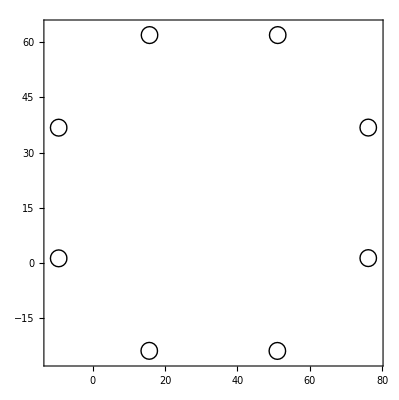

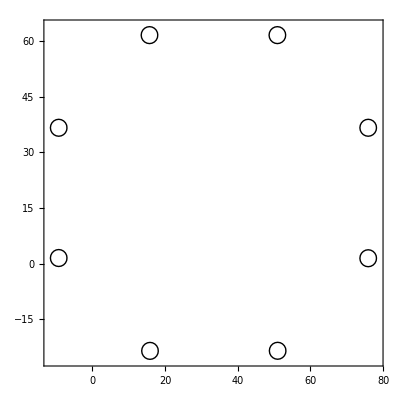

```mathematica
Print[Graphics[#,Frame->True]]&/@holes;
```

```mathematica
holepolygons=Map[StringReplace[StringReplace[ToString[#],{"Line["->"polygon(","]"->");"}],{"{"->"[","}"->"]"}]&,holes,{2}]
```

{{polygon([[78.4606, 36.7792], [78.3487, 37.4856], [78.024, 38.1229], [77.5183, 38.6286], [76.881, 38.9533], [76.1746, 39.0652], [75.4682, 38.9533], [74.8309, 38.6286], [74.3252, 38.1229], [74.0005, 37.4856], [73.8886, 36.7792], [74.0005, 36.0728], [74.3252, 35.4355], [74.8309, 34.9298], [75.4682, 34.6051], [76.1746, 34.4932], [76.881, 34.6051], [77.5183, 34.9298], [78.024, 35.4355], [78.3487, 36.0728], [78.4606, 36.7792]]);,polygon([[78.4606, 1.3558], [78.3487, 2.06221], [78.024, 2.69948], [77.5183, 3.20521], [76.881, 3.52992], [76.1746, 3.6418], [75.4682, 3.52992], [74.8309, 3.20521], [74.3252, 2.69948], [74.0005, 2.06221], [73.8886, 1.3558], [74.0005, 0.649387], [74.3252, 0.0121229], [74.8309, -0.493613], [75.4682, -0.818315], [76.1746, -0.9302], [76.881, -0.818315], [77.5183, -0.493613], [78.024, 0.0121229], [78.3487, 0.649387], [78.4606, 1.3558]]);,polygon([[17.9832, 61.8758], [17.8713, 62.5822], [17.5466, 63.2195], [17.0409, 63.7252], [16.4036, 64.0499], [15.6972, 64.1618], [14.9908, 64.0499], [14.3535, 63.7252], [13.8478, 63.2195], [13.5231, 62.5822], [13.4112, 61.8758], [13.5231, 61.1694], [13.8478, 60.5321], [14.3535, 60.0264], [14.9908, 59.7017], [15.6972, 59.5898], [16.4036, 59.7017], [17.0409, 60.0264], [17.5466, 60.5321], [17.8713, 61.1694], [17.9832, 61.8758]]);,polygon([[53.3304, -23.825], [53.2185, -23.1186], [52.8938, -22.4813], [52.3881, -21.9756], [51.7508, -21.6509], [51.0444, -21.539], [50.338, -21.6509], [49.7007, -21.9756], [49.195, -22.4813], [48.8703, -23.1186], [48.7584, -23.825], [48.8703, -24.5314], [49.195, -25.1687], [49.7007, -25.6744], [50.338, -25.9991], [51.0444, -26.111], [51.7508, -25.9991], [52.3881, -25.6744], [52.8938, -25.1687], [53.2185, -24.5314], [53.3304, -23.825]]);,polygon([[17.907, -23.7998], [17.7951, -23.0934], [17.4704, -22.4561], [16.9647, -21.9504], [16.3274, -21.6257], [15.621, -21.5138], [14.9146, -21.6257], [14.2773, -21.9504], [13.7716, -22.4561], [13.4469, -23.0934], [13.335, -23.7998], [13.4469, -24.5062], [13.7716, -25.1435], [14.2773, -25.6492], [14.9146, -25.9739], [15.621, -26.0858], [16.3274, -25.9739], [16.9647, -25.6492], [17.4704, -25.1435], [17.7951, -24.5062], [17.907, -23.7998]]);,polygon([[-7.1374, 1.2954], [-7.24928, 2.00181], [-7.57399, 2.63908], [-8.07972, 3.14481], [-8.71699, 3.46952], [-9.4234, 3.5814], [-10.1298, 3.46952], [-10.7671, 3.14481], [-11.2728, 2.63908], [-11.5975, 2.00181], [-11.7094, 1.2954], [-11.5975, 0.588987], [-11.2728, -0.0482771], [-10.7671, -0.554013], [-10.1298, -0.878715], [-9.4234, -0.9906], [-8.71699, -0.878715], [-8.07972, -0.554013], [-7.57399, -0.0482771], [-7.24928, 0.588987], [-7.1374, 1.2954]]);,polygon([[-7.1374, 36.7538], [-7.24928, 37.4602], [-7.57399, 38.0975], [-8.07972, 38.6032], [-8.71699, 38.9279], [-9.4234, 39.0398], [-10.1298, 38.9279], [-10.7671, 38.6032], [-11.2728, 38.0975], [-11.5975, 37.4602], [-11.7094, 36.7538], [-11.5975, 36.0474], [-11.2728, 35.4101], [-10.7671, 34.9044], [-10.1298, 34.5797], [-9.4234, 34.4678], [-8.71699, 34.5797], [-8.07972, 34.9044], [-7.57399, 35.4101], [-7.24928, 36.0474], [-7.1374, 36.7538]]);,polygon([[53.4288, 61.8758], [53.3169, 62.5822], [52.9922, 63.2195], [52.4865, 63.7252], [51.8492, 64.0499], [51.1428, 64.1618], [50.4364, 64.0499], [49.7991, 63.7252], [49.2934, 63.2195], [48.9687, 62.5822], [48.8568, 61.8758], [48.9687, 61.1694], [49.2934, 60.5321], [49.7991, 60.0264], [50.4364, 59.7017], [51.1428, 59.5898], [51.8492, 59.7017], [52.4865, 60.0264], [52.9922, 60.5321], [53.3169, 61.1694], [53.4288, 61.8758]]);},{polygon([[-6.9596, 36.6268], [-7.07148, 37.3332], [-7.39619, 37.9705], [-7.90192, 38.4762], [-8.53919, 38.8009], [-9.2456, 38.9128], [-9.95201, 38.8009], [-10.5893, 38.4762], [-11.095, 37.9705], [-11.4197, 37.3332], [-11.5316, 36.6268], [-11.4197, 35.9204], [-11.095, 35.2831], [-10.5893, 34.7774], [-9.95201, 34.4527], [-9.2456, 34.3408], [-8.53919, 34.4527], [-7.90192, 34.7774], [-7.39619, 35.2831], [-7.07148, 35.9204], [-6.9596, 36.6268]]);,polygon([[-6.9596, 1.4828], [-7.07148, 2.18921], [-7.39619, 2.82648], [-7.90192, 3.33221], [-8.53919, 3.65692], [-9.2456, 3.7688], [-9.95201, 3.65692], [-10.5893, 3.33221], [-11.095, 2.82648], [-11.4197, 2.18921], [-11.5316, 1.4828], [-11.4197, 0.776387], [-11.095, 0.139123], [-10.5893, -0.366613], [-9.95201, -0.691315], [-9.2456, -0.8032], [-8.53919, -0.691315], [-7.90192, -0.366613], [-7.39619, 0.139123], [-7.07148, 0.776387], [-6.9596, 1.4828]]);,polygon([[53.213, 61.6218], [53.1011, 62.3282], [52.7764, 62.9655], [52.2707, 63.4712], [51.6334, 63.7959], [50.927, 63.9078], [50.2206, 63.7959], [49.5833, 63.4712], [49.0776, 62.9655], [48.7529, 62.3282], [48.641, 61.6218], [48.7529, 60.9154], [49.0776, 60.2781], [49.5833, 59.7724], [50.2206, 59.4477], [50.927, 59.3358], [51.6334, 59.4477], [52.2707, 59.7724], [52.7764, 60.2781], [53.1011, 60.9154], [53.213, 61.6218]]);,polygon([[18.161, -23.571], [18.0491, -22.8646], [17.7244, -22.2273], [17.2187, -21.7216], [16.5814, -21.3969], [15.875, -21.285], [15.1686, -21.3969], [14.5313, -21.7216], [14.0256, -22.2273], [13.7009, -22.8646], [13.589, -23.571], [13.7009, -24.2774], [14.0256, -24.9147], [14.5313, -25.4204], [15.1686, -25.7451], [15.875, -25.857], [16.5814, -25.7451], [17.2187, -25.4204], [17.7244, -24.9147], [18.0491, -24.2774], [18.161, -23.571]]);,polygon([[53.2892, -23.5458], [53.1773, -22.8394], [52.8526, -22.2021], [52.3469, -21.6964], [51.7096, -21.3717], [51.0032, -21.2598], [50.2968, -21.3717], [49.6595, -21.6964], [49.1538, -22.2021], [48.8291, -22.8394], [48.7172, -23.5458], [48.8291, -24.2522], [49.1538, -24.8895], [49.6595, -25.3952], [50.2968, -25.7199], [51.0032, -25.8318], [51.7096, -25.7199], [52.3469, -25.3952], [52.8526, -24.8895], [53.1773, -24.2522], [53.2892, -23.5458]]);,polygon([[78.2066, 1.4224], [78.0947, 2.12881], [77.77, 2.76608], [77.2643, 3.27181], [76.627, 3.59652], [75.9206, 3.7084], [75.2142, 3.59652], [74.5769, 3.27181], [74.0712, 2.76608], [73.7465, 2.12881], [73.6346, 1.4224], [73.7465, 0.715987], [74.0712, 0.0787229], [74.5769, -0.427013], [75.2142, -0.751715], [75.9206, -0.8636], [76.627, -0.751715], [77.2643, -0.427013], [77.77, 0.0787229], [78.0947, 0.715987], [78.2066, 1.4224]]);,polygon([[78.2066, 36.6268], [78.0947, 37.3332], [77.77, 37.9705], [77.2643, 38.4762], [76.627, 38.8009], [75.9206, 38.9128], [75.2142, 38.8009], [74.5769, 38.4762], [74.0712, 37.9705], [73.7465, 37.3332], [73.6346, 36.6268], [73.7465, 35.9204], [74.0712, 35.2831], [74.5769, 34.7774], [75.2142, 34.4527], [75.9206, 34.3408], [76.627, 34.4527], [77.2643, 34.7774], [77.77, 35.2831], [78.0947, 35.9204], [78.2066, 36.6268]]);,polygon([[18.0214, 61.6218], [17.9095, 62.3282], [17.5848, 62.9655], [17.0791, 63.4712], [16.4418, 63.7959], [15.7354, 63.9078], [15.029, 63.7959], [14.3917, 63.4712], [13.886, 62.9655], [13.5613, 62.3282], [13.4494, 61.6218], [13.5613, 60.9154], [13.886, 60.2781], [14.3917, 59.7724], [15.029, 59.4477], [15.7354, 59.3358], [16.4418, 59.4477], [17.0791, 59.7724], [17.5848, 60.2781], [17.9095, 60.9154], [18.0214, 61.6218]]);}}

```mathematica
MapThread[Export[#1,#2,"Text"]&,{StringReplace[feilen,"dxf"->"2holes.scad"],holepolygons}]
```

{sinobit_v1.0.2holes.scad,sinobit_v1.1.2holes.scad}

## Sinobit from numbers

```mathematica
width=3.625 2.54
```

9.2075

```mathematica
CirclePoints[8]
```

{{Sin[π/8],-Cos[π/8]},{Cos[π/8],-Sin[π/8]},{Cos[π/8],Sin[π/8]},{Sin[π/8],Cos[π/8]},{-Sin[π/8],Cos[π/8]},{-Cos[π/8],Sin[π/8]},{-Cos[π/8],-Sin[π/8]},{-Sin[π/8],-Cos[π/8]}}

```mathematica
CirclePoints[8]/(2 Cos[π/8])
```

{{1/2 Tan[π/8],-1/2},{1/2,-1/2 Tan[π/8]},{1/2,1/2 Tan[π/8]},{1/2 Tan[π/8],1/2},{-1/2 Tan[π/8],1/2},{-1/2,1/2 Tan[π/8]},{-1/2,-1/2 Tan[π/8]},{-1/2 Tan[π/8],-1/2}}

```mathematica
N[π/8/°]
```

22.5